## Graph

### 1.1 Relations of h and R1

#### Graph

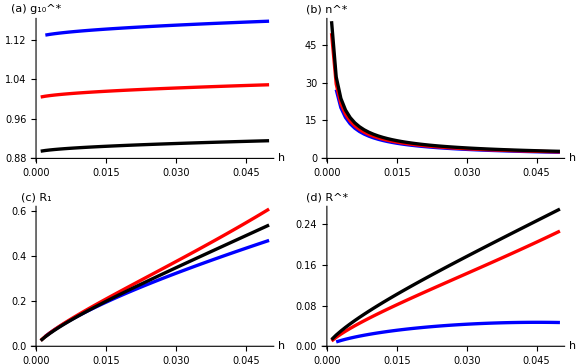

C:\Users\June\Desktop\June\draft8 -check\Section 4\5. Figures\5. figures\Vhtest.png

```mathematica
VRdatahtestXY=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatahtestXY.xlsx"][[1]];
VRdatahtestXZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatahtestXZ.xlsx"][[1]];
VRdatahtestYZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatahtestYZ.xlsx"][[1]];


thinPlotStyle={Directive[Blue,Thickness[0.006]],Directive[Red,Thickness[0.006]],Directive[Black,Thickness[0.006]]};


Vhg10=Show[ListPlot[{VRdatahtestXY[[All,{1,2}]],VRdatahtestXZ[[All,{1,2}]],VRdatahtestYZ[[All,{1,2}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["h",15],Style["(a) \!\(\*SubsuperscriptBox[\(g\), \(10\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


Vhn=Show[ListPlot[{VRdatahtestXY[[All,{1,3}]],VRdatahtestXZ[[All,{1,3}]],VRdatahtestYZ[[All,{1,3}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["h",15],Style["(b) \!\(\*SuperscriptBox[\(n\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


VhR1=Show[ListPlot[{VRdatahtestXY[[All,{1,4}]],VRdatahtestXZ[[All,{1,4}]],VRdatahtestYZ[[All,{1,4}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["h",15],Style["(c) R_1",15]},TicksStyle->Directive[14]]];


VhR=Show[ListPlot[{VRdatahtestXY[[All,{1,5}]],VRdatahtestXZ[[All,{1,5}]],VRdatahtestYZ[[All,{1,5}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["h",15],Style["(d) \!\(\*SuperscriptBox[\(R\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


panelh=GraphicsGrid[{{Vhg10,Vhn},{VhR1,VhR}},Spacings->{Scaled[0.03],Scaled[0.1]},ImageSize->Large];


legend=LineLegend[thinPlotStyle,{"XY fiber","XZ fiber","YZ fiber"}];


Vhtest=Labeled[panelh,legend,{Right,Top}]

dirVhtest=FileNameJoin[{NotebookDirectory[],"5. figures"}];

If[!DirectoryQ[dirVhtest],CreateDirectory[dirVhtest]];

Export[FileNameJoin[{dirVhtest,"Vhtest.png"}],Vhtest,ImageResolution->300]
```

### 1.2 Relations of g30 and R1

#### Graph

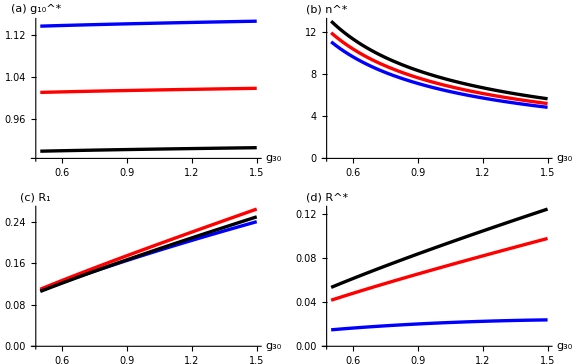

C:\Users\June\Desktop\June\draft8 -check\Section 4\5. Figures\5. figures\Vg30test.png

```mathematica
VRdatag30testXY=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatag30testXY.xlsx"][[1]];
VRdatag30testXZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatag30testXZ.xlsx"][[1]];
VRdatag30testYZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatag30testYZ.xlsx"][[1]];




thinPlotStyle={Directive[Blue,Thickness[0.006]],Directive[Red,Thickness[0.006]],Directive[Black,Thickness[0.006]]};


Vg30g10=Show[ListPlot[{VRdatag30testXY[[All,{1,2}]],VRdatag30testXZ[[All,{1,2}]],VRdatag30testYZ[[All,{1,2}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["g_30",15],Style["(a) \!\(\*SubsuperscriptBox[\(g\), \(10\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


Vg30n=Show[ListPlot[{VRdatag30testXY[[All,{1,3}]],VRdatag30testXZ[[All,{1,3}]],VRdatag30testYZ[[All,{1,3}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["g_30",15],Style["(b) \!\(\*SuperscriptBox[\(n\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


Vg30R1=Show[ListPlot[{VRdatag30testXY[[All,{1,4}]],VRdatag30testXZ[[All,{1,4}]],VRdatag30testYZ[[All,{1,4}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["g_30",15],Style["(c) R_1",15]},TicksStyle->Directive[14]]];


Vg30R=Show[ListPlot[{VRdatag30testXY[[All,{1,5}]],VRdatag30testXZ[[All,{1,5}]],VRdatag30testYZ[[All,{1,5}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["g_30",15],Style["(d) \!\(\*SuperscriptBox[\(R\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


panelg30=GraphicsGrid[{{Vg30g10,Vg30n},{Vg30R1,Vg30R}},Spacings->{Scaled[0.03],Scaled[0.1]},ImageSize->Large];



legend=LineLegend[thinPlotStyle,{"XY fiber","XZ fiber","YZ fiber"}];

Vg30test=Labeled[panelg30,legend,{Right,Top}]

dirVg30test=FileNameJoin[{NotebookDirectory[],"5. figures"}];

If[!DirectoryQ[dirVg30test],CreateDirectory[dirVg30test]];

Export[FileNameJoin[{dirVg30test,"Vg30test.png"}],Vg30test,ImageResolution->300]
```

### 1.3 Relations of KK and R1

#### Graph

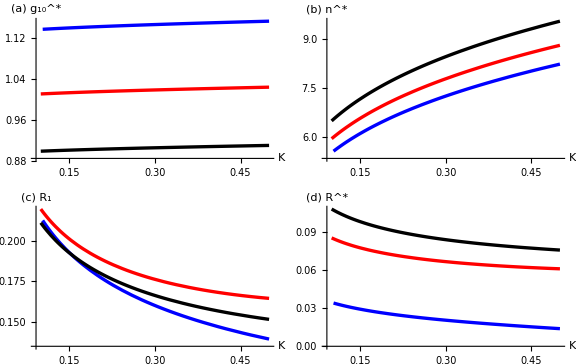

C:\Users\June\Desktop\June\draft8 -check\Section 4\5. Figures\5. figures\VKKtest.png

```mathematica
VRdataKKtestXY=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdataKKtestXY.xlsx"][[1]];
VRdataKKtestXZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdataKKtestXZ.xlsx"][[1]];
VRdataKKtestYZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdataKKtestYZ.xlsx"][[1]];




thinPlotStyle={Directive[Blue,Thickness[0.006]],Directive[Red,Thickness[0.006]],Directive[Black,Thickness[0.006]]};


VKKg10=Show[ListPlot[{VRdataKKtestXY[[All,{1,2}]],VRdataKKtestXZ[[All,{1,2}]],VRdataKKtestYZ[[All,{1,2}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["K",15],Style["(a) \!\(\*SubsuperscriptBox[\(g\), \(10\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


VKKn=Show[ListPlot[{VRdataKKtestXY[[All,{1,3}]],VRdataKKtestXZ[[All,{1,3}]],VRdataKKtestYZ[[All,{1,3}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["K",15],Style["(b) \!\(\*SuperscriptBox[\(n\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


VKKR1=Show[ListPlot[{VRdataKKtestXY[[All,{1,4}]],VRdataKKtestXZ[[All,{1,4}]],VRdataKKtestYZ[[All,{1,4}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["K",15],Style["(c) R_1",15]},TicksStyle->Directive[14]]];


VKKR=Show[ListPlot[{VRdataKKtestXY[[All,{1,5}]],VRdataKKtestXZ[[All,{1,5}]],VRdataKKtestYZ[[All,{1,5}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["K",15],Style["(d) \!\(\*SuperscriptBox[\(R\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


panelKK=GraphicsGrid[{{VKKg10,VKKn},{VKKR1,VKKR}},Spacings->{Scaled[0.03],Scaled[0.1]},ImageSize->Large];


legend=LineLegend[thinPlotStyle,{"XY fiber","XZ fiber","YZ fiber"}];


VKKtest=Labeled[panelKK,legend,{Right,Top}]

dirVKKtest=FileNameJoin[{NotebookDirectory[],"5. figures"}];

If[!DirectoryQ[dirVKKtest],CreateDirectory[dirVKKtest]];

Export[FileNameJoin[{dirVKKtest,"VKKtest.png"}],VKKtest,ImageResolution->300]
```

### 2.1 Relations of beta and R1

#### Graph

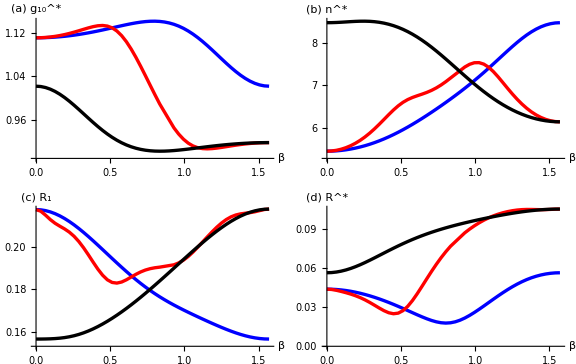

C:\Users\June\Desktop\June\draft8 -check\Section 4\5. Figures\5. figures\Vbetatest.png

```mathematica
VRdatabetatestXY=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatabetatestXY.xlsx"][[1]];
VRdatabetatestXZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatabetatestXZ.xlsx"][[1]];
VRdatabetatestYZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatabetatestYZ.xlsx"][[1]];




thinPlotStyle={Directive[Blue,Thickness[0.006]],Directive[Red,Thickness[0.006]],Directive[Black,Thickness[0.006]]};


Vbetag10=Show[ListPlot[{VRdatabetatestXY[[All,{1,2}]],VRdatabetatestXZ[[All,{1,2}]],VRdatabetatestYZ[[All,{1,2}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["β",15],Style["(a) \!\(\*SubsuperscriptBox[\(g\), \(10\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


Vbetan=Show[ListPlot[{VRdatabetatestXY[[All,{1,3}]],VRdatabetatestXZ[[All,{1,3}]],VRdatabetatestYZ[[All,{1,3}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["β",15],Style["(b) \!\(\*SuperscriptBox[\(n\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


VbetaR1=Show[ListPlot[{VRdatabetatestXY[[All,{1,4}]],VRdatabetatestXZ[[All,{1,4}]],VRdatabetatestYZ[[All,{1,4}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["β",15],Style["(c) R_1",15]},TicksStyle->Directive[14]]];


VbetaR=Show[ListPlot[{VRdatabetatestXY[[All,{1,5}]],VRdatabetatestXZ[[All,{1,5}]],VRdatabetatestYZ[[All,{1,5}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["β",15],Style["(d) \!\(\*SuperscriptBox[\(R\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


panelbeta=GraphicsGrid[{{Vbetag10,Vbetan},{VbetaR1,VbetaR}},Spacings->{Scaled[0.03],Scaled[0.1]},ImageSize->Large];


legend=LineLegend[thinPlotStyle,{"XY fiber","XZ fiber","YZ fiber"}];


Vbetatest=Labeled[panelbeta,legend,{Right,Top}]

dirVbetatest=FileNameJoin[{NotebookDirectory[],"5. figures"}];

If[!DirectoryQ[dirVbetatest],CreateDirectory[dirVbetatest]];

Export[FileNameJoin[{dirVbetatest,"Vbetatest.png"}],Vbetatest,ImageResolution->300]
```

### 2.2 Relations of lamdaf and R1

#### Graph

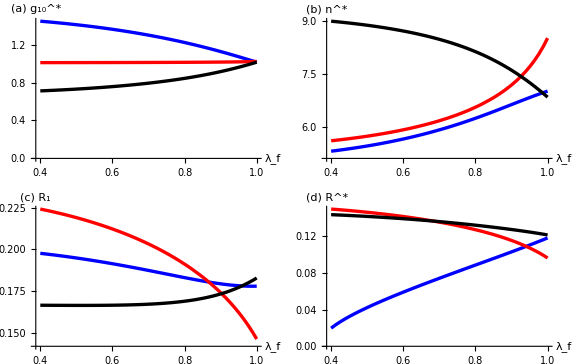

C:\Users\June\Desktop\June\draft8 -check\Section 4\5. Figures\5. figures\Vlamdaftest.png

```mathematica
VRdatalamdaftestXY=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatalamdaftestXY.xlsx"][[1]];
VRdatalamdaftestXZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatalamdaftestXZ.xlsx"][[1]];
VRdatalamdaftestYZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatalamdaftestYZ.xlsx"][[1]];





thinPlotStyle={Directive[Blue,Thickness[0.006]],Directive[Red,Thickness[0.006]],Directive[Black,Thickness[0.006]]};


Vlamdafg10=Show[ListPlot[{VRdatalamdaftestXY[[All,{1,2}]],VRdatalamdaftestXZ[[All,{1,2}]],VRdatalamdaftestYZ[[All,{1,2}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["λ_f",15],Style["(a) \!\(\*SubsuperscriptBox[\(g\), \(10\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


Vlamdafn=Show[ListPlot[{VRdatalamdaftestXY[[All,{1,3}]],VRdatalamdaftestXZ[[All,{1,3}]],VRdatalamdaftestYZ[[All,{1,3}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["λ_f",15],Style["(b) \!\(\*SuperscriptBox[\(n\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


VlamdafR1=Show[ListPlot[{VRdatalamdaftestXY[[All,{1,4}]],VRdatalamdaftestXZ[[All,{1,4}]],VRdatalamdaftestYZ[[All,{1,4}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["λ_f",15],Style["(c) R_1",15]},TicksStyle->Directive[14]]];


VlamdafR=Show[ListPlot[{VRdatalamdaftestXY[[All,{1,5}]],VRdatalamdaftestXZ[[All,{1,5}]],VRdatalamdaftestYZ[[All,{1,5}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["λ_f",15],Style["(d) \!\(\*SuperscriptBox[\(R\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


panellamdaf=GraphicsGrid[{{Vlamdafg10,Vlamdafn},{VlamdafR1,VlamdafR}},Spacings->{Scaled[0.03],Scaled[0.1]},ImageSize->Large];


legend=LineLegend[thinPlotStyle,{"XY fiber","XZ fiber","YZ fiber"}];


Vlamdaftest=Labeled[panellamdaf,legend,{Right,Top}]

dirVlamdaftest=FileNameJoin[{NotebookDirectory[],"5. figures"}];

If[!DirectoryQ[dirVlamdaftest],CreateDirectory[dirVlamdaftest]];

Export[FileNameJoin[{dirVlamdaftest,"Vlamdaftest.png"}],Vlamdaftest,ImageResolution->300]
```

### 2.3 Relations of cf and R1

#### Graph

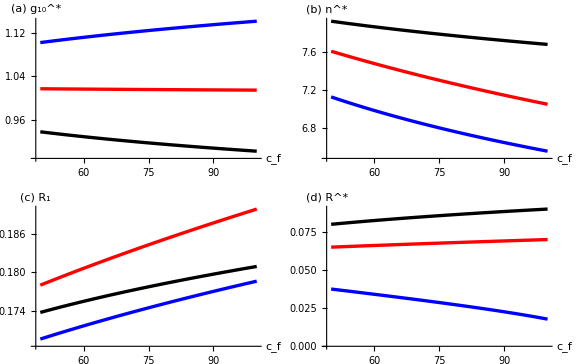

C:\Users\June\Desktop\June\draft8 -check\Section 4\5. Figures\5. figures\Vcftest.png

```mathematica
VRdatacftestXY=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdatacftestXY.xlsx"][[1]];
VRdatacftestXZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdatacftestXZ.xlsx"][[1]];
VRdatacftestYZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdatacftestYZ.xlsx"][[1]];




thinPlotStyle={Directive[Blue,Thickness[0.006]],Directive[Red,Thickness[0.006]],Directive[Black,Thickness[0.006]]};


Vcfg10=Show[ListPlot[{VRdatacftestXY[[All,{1,2}]],VRdatacftestXZ[[All,{1,2}]],VRdatacftestYZ[[All,{1,2}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["c_f",15],Style["(a) \!\(\*SubsuperscriptBox[\(g\), \(10\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


Vcfn=Show[ListPlot[{VRdatacftestXY[[All,{1,3}]],VRdatacftestXZ[[All,{1,3}]],VRdatacftestYZ[[All,{1,3}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["c_f",15],Style["(b) \!\(\*SuperscriptBox[\(n\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


VcfR1=Show[ListPlot[{VRdatacftestXY[[All,{1,4}]],VRdatacftestXZ[[All,{1,4}]],VRdatacftestYZ[[All,{1,4}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["c_f",15],Style["(c) R_1",15]},TicksStyle->Directive[14]]];


VcfR=Show[ListPlot[{VRdatacftestXY[[All,{1,5}]],VRdatacftestXZ[[All,{1,5}]],VRdatacftestYZ[[All,{1,5}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["c_f",15],Style["(d) \!\(\*SuperscriptBox[\(R\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


panelcf=GraphicsGrid[{{Vcfg10,Vcfn},{VcfR1,VcfR}},Spacings->{Scaled[0.03],Scaled[0.1]},ImageSize->Large];


legend=LineLegend[thinPlotStyle,{"XY fiber","XZ fiber","YZ fiber"}];


Vcftest=Labeled[panelcf,legend,{Right,Top}]

dirVcftest=FileNameJoin[{NotebookDirectory[],"5. figures"}];

If[!DirectoryQ[dirVcftest],CreateDirectory[dirVcftest]];

Export[FileNameJoin[{dirVcftest,"Vcftest.png"}],Vcftest,ImageResolution->300]
```

### 2.4 Relations of phif and R1

#### Graph

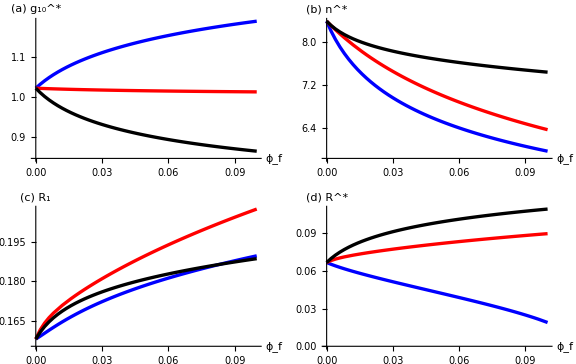

C:\Users\June\Desktop\June\draft8 -check\Section 4\5. Figures\5. figures\Vphiftest.png

```mathematica
VRdataphiftestXY=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.1 XY_data\\VRdataphiftestXY.xlsx"][[1]];
VRdataphiftestXZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.2 XZ_data\\VRdataphiftestXZ.xlsx"][[1]];
VRdataphiftestYZ=Import["C:\\Users\\June\\Desktop\\June\\draft8 -check\\Section 4\\4. XY_data & XZ_data & YZ_data\\4.3 YZ_data\\VRdataphiftestYZ.xlsx"][[1]];




thinPlotStyle={Directive[Blue,Thickness[0.006]],Directive[Red,Thickness[0.006]],Directive[Black,Thickness[0.006]]};


Vphifg10=Show[ListPlot[{VRdataphiftestXY[[All,{1,2}]],VRdataphiftestXZ[[All,{1,2}]],VRdataphiftestYZ[[All,{1,2}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["ϕ_f",15],Style["(a) \!\(\*SubsuperscriptBox[\(g\), \(10\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


Vphifn=Show[ListPlot[{VRdataphiftestXY[[All,{1,3}]],VRdataphiftestXZ[[All,{1,3}]],VRdataphiftestYZ[[All,{1,3}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["ϕ_f",15],Style["(b) \!\(\*SuperscriptBox[\(n\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


VphifR1=Show[ListPlot[{VRdataphiftestXY[[All,{1,4}]],VRdataphiftestXZ[[All,{1,4}]],VRdataphiftestYZ[[All,{1,4}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["ϕ_f",15],Style["(c) R_1",15]},TicksStyle->Directive[14]]];


VphifR=Show[ListPlot[{VRdataphiftestXY[[All,{1,5}]],VRdataphiftestXZ[[All,{1,5}]],VRdataphiftestYZ[[All,{1,5}]]},Joined->True,PlotStyle->thinPlotStyle,PlotRange->All,AxesLabel->{Style["ϕ_f",15],Style["(d) \!\(\*SuperscriptBox[\(R\), \(*\)]\)",15]},TicksStyle->Directive[14]]];


panelphif=GraphicsGrid[{{Vphifg10,Vphifn},{VphifR1,VphifR}},Spacings->{Scaled[0.03],Scaled[0.1]},ImageSize->Large];


legend=LineLegend[thinPlotStyle,{"XY fiber","XZ fiber","YZ fiber"}];


Vphiftest=Labeled[panelphif,legend,{Right,Top}]

dirVphiftest=FileNameJoin[{NotebookDirectory[],"5. figures"}];

If[!DirectoryQ[dirVphiftest],CreateDirectory[dirVphiftest]];

Export[FileNameJoin[{dirVphiftest,"Vphiftest.png"}],Vphiftest,ImageResolution->300]
```